```mathematica
Exit[]
```

# Gamma gq

```mathematica
<<"/Users/giacomomagni/Documents/Wolfram Mathematica/Sigma.m"
<<"/Users/giacomomagni/Documents/Wolfram Mathematica/HarmonicSums.m"
LaunchKernels[4];
```

Sigma - A summation package by Carsten Schneider — © RISC —  V 2.86 (June 15, 2021)  Help

HarmonicSums by Jakob Ablinger — © RISC — Version 1.0(30/03/21)Help

#### Inputs

```mathematica
here = NotebookDirectory[];
Get[StringJoin[here, "constants.m"]]
```

```mathematica
(* Singlet, large nf exact parts *)
Get[StringJoin[here, "singlet_nf3.m"]]
Get[StringJoin[here, "ns_nf3_nf2.m"]]
(* Singlet, asymptotic N-> Infinity, large nc limit *)
Get[StringJoin[here, "qcd_cusp.m"]]
(* Singlet, moments *)
Get[StringJoin[here, "gqq3nsp.m"]]
Get[StringJoin[here, "gqq3ps.m"]]
Get[StringJoin[here, "gqg3.m"]]
Get[StringJoin[here, "ggq3.m"]]
Get[StringJoin[here, "ggg3.m"]]
```

```mathematica
Get[StringJoin[here, "fitting_utils.m"]]
Get[StringJoin[here, "plotting_utils.m"]]
Get[StringJoin[here, "saving_utils.m"]]
```

#### Cross candidates

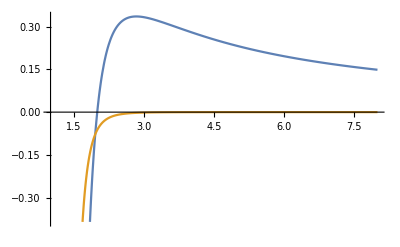

```mathematica
Plot[{S[3,n-2]/n /. InverseHarmonicRules, -1/(n^4(n-1)^3)}, {n,1,8}]
```

```mathematica
thrhigh = 10^-7;
thrlow = 10^-3;
ggqmoments = {ggq3N2,ggq3N4,ggq3N6,ggq3N8};

fsmallN = {
	(* 1/(n-1)^3, 1/(n-1)^3, 1/(n-1)^2, 1/(n-1)*)
	(* Note S[1,n-2]/n has a large-x divergence, can't use it here*)
	(* In order to proberly account for the scaling cf/ca P_gg,
	we assume no violation on the sacling in the part prorportional to nf^0.
	This sould be consistent with what is happening at NNLO. *)
	S[2,n-2]/n, S[3,n-2]/n, S[2,n-2]/n, 1/(n-1)
};
flargeN = {S13m1[n],S13m1[n],S13m1[n],S13m1[n]};

fSubLeadingLargeN = {
	{1/(n+1),1/(n+1),1/(n+1),1/(n+1)},
	{1/(n+2),1/(n+2),1/(n+2),1/(n+2)}
	(* {1/(n+1)^2,1/(n+1)^2,1/(n+1)^2,1/(n+1)^2}, 
	{1/(n+1)^3,1/(n+1)^3,1/(n+1)^3,1/(n+1)^3},*)
	(*{Lm11[n],Lm11[n],Lm11[n], Lm11[n]}, 
	{Lm12[n],Lm12[n],Lm12[n], Lm12[n]}, 
	{Lm13[n],Lm13[n],Lm13[n], Lm13[n]},
	{S12m1[n],S12m1[n],S12m1[n],S12m1[n]},
	{S[1,n-2]/n, S[1,n-2]/n, S[1,n-2]/n, 1/n}*)
};
fSubLeadingSmallN = {
	(* Apparently fitting 1/(n-1)^2 makes the nf1 and nf0 part not smooth anymore in N space ...*)
	(* {S[2,n-2]/n, S[2,n-2]/n, S[1,n-2]/n, 1/n},*)
	{1/(n-1),S[2,n-2]/n,1/(n-1),1/(n-1)},
	{1/n^4,1/n^4,1/n^4,1/n^4},
	{1/n^3,1/n^3,1/n^3,1/n^3},
	{1/n^2,1/n^2,1/n^2,1/n^2},
	{1/n,1/n,1/n,1/n,1/n}
};

ggq3N1asyImproved = ggq3N1asy + cf/ca Coefficient[ggg3N1asy /. nf -> 0, (n-1), -3] 1/(n-1)^3;
ggq3asy = MellinInverseSinglet[ggq3N0asy + ggq3N1asyImproved + ggq3Ninf] /. Delta[x__] -> 0 /. LimitRules /. ZetaRules;
```

```mathematica
fSubLeadingtot = Join[fSubLeadingSmallN, fSubLeadingLargeN];
ggq3FittedCross = DoAllFits[fsmallN, flargeN, fSubLeadingtot, ggqmoments, ggq3N0asy, ggq3N1asyImproved, ggq3Ninf];
(* PlotRelativeDiffIterate[ggq3nf3 , ggq3FittedCross + Coefficient[ggq3N0asy +ggq3Ninf, nf ,3], 3, 2, 6]*)
ggq3invfull = ListMellinInverse[ggq3FittedCross];
ggq3inv = SelectSmoothCandidates[ggq3invfull, 4,thrlow,thrlow];
graphGQrep = PlotList[ggq3inv, ggq3asy, 4, 3];
graphGQlogrep = LogPlotList[ggq3inv, ggq3asy, 4, 3];
graphGQloglargerep = LogPlotListLargeX[ggq3inv, ggq3asy, 4, 3] // Show;
GraphicsRow[{graphGQlogrep // Show,Show[graphGQrep, PlotRange-> {Automatic,{-0.01, 0.01}}], graphGQloglargerep}]
```

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

Part::partd: Part specification Null⟦2⟧ is longer than depth of object.

Part::partd: Part specification Null⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

General::stop: Further output of Fit::fitm will be suppressed during this calculation.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

General::stop: Further output of Fit::fitm will be suppressed during this calculation.

General::ivar: 1+n is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

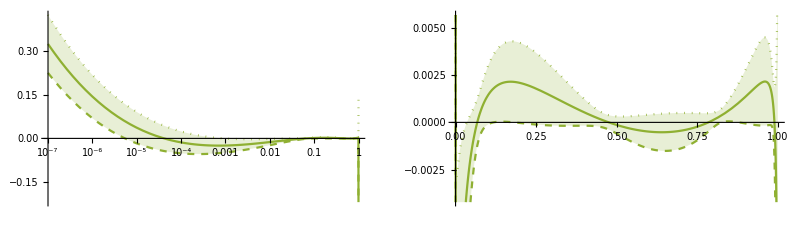

```mathematica
{graphGQ,graphGQlog} =  PlotErrorBand[ggq3asy, ggq3inv, 4, 3];
GraphicsRow[{graphGQlog,graphGQ}]
```

#### Cherry Picking

```mathematica
cherryfunctions = {1/(n-1), 1/n^4};
ggq3cherry = SelectCherries[ggq3FittedCross, cherryfunctions];
ggq3cherry = SelectSmoothCandidates[ggq3cherry, 4, thrlow, thrhigh];
```

Selected cherries are: 25 out of 91

Smooth candidates: 24 out of 25

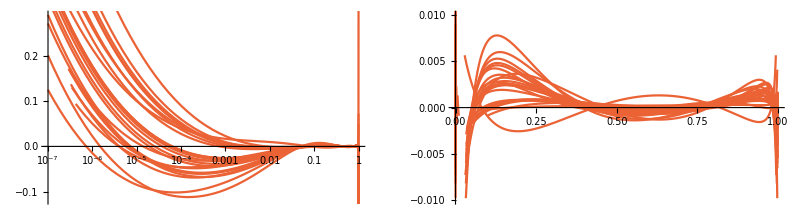

```mathematica
graphGQcherryrep = PlotList[ggq3cherry, ggq3asy, 4, 4];
graphGQlogcherryrep = LogPlotList[ggq3cherry, ggq3asy, 4, 4];
GraphicsRow[{graphGQlogcherryrep // Show, Show[graphGQcherryrep, PlotRange -> {Automatic, {-0.01, 0.01}}]}]
```

```mathematica
{graphGQcherry, graphGQcherrylog} = PlotErrorBand[ggq3asy, ggq3cherry, 4, 4]; 
legend = {"cross candidate", "cherries"}; 
GraphicsRow[{
    	ShowLegends[{graphGQlog, graphGQcherrylog}, LogLinearPlot, legend, {3, 4}], 
    	ShowLegends[{graphGQ, graphGQcherry}, Plot, legend, {3, 4}]
    	}, ImageSize -> Full
 ]
```

-Graphics-

#### Plot nf^3

```mathematica
ggq3asy3 = Coefficient[ggq3asy, nf, 3];
ggq3inv3 =  SelectSmoothCandidates[Coefficient[ggq3inv, nf, 3], 4,thrlow,thrlow];
ggq3inv3cherries =  SelectSmoothCandidates[Coefficient[ggq3cherry, nf, 3], 4,thrlow,thrlow];
ggq3nf3x = ggq3nf3x /. QCDConstantsRules //N;
```

Smooth candidates: 86 out of 87

Smooth candidates: 22 out of 24

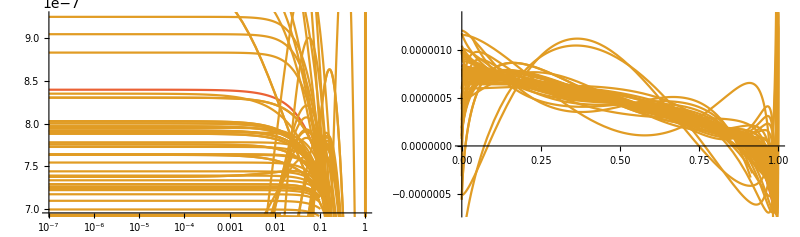

```mathematica
gtmp = PlotList[ggq3inv3, ggq3asy3, 4, 2];
gtmplog = LogPlotList[ggq3inv3, ggq3asy3, 4, 2];
graphGQExa3 = Plot[pifact ggq3nf3x, {x, 0, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
graphGQExa3log = LogLinearPlot[ pifact ggq3nf3x, {x, 10^-7, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
GraphicsRow[{Show[{graphGQExa3log, gtmplog}], Show[{graphGQExa3, gtmp}]}, ImageSize->Full]
```

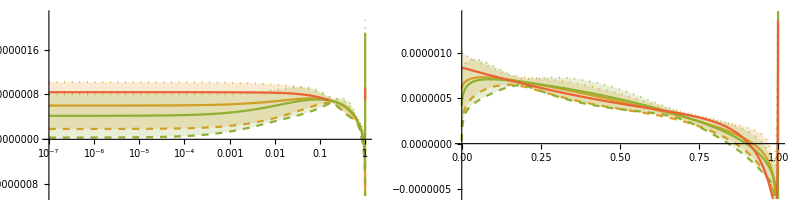

```mathematica
{graphGQ3, graphGQ3log} = PlotErrorBand[ggq3asy3, ggq3inv3, 4,2];
{graphGQ3cherry, graphGQ3cherrylog} = PlotErrorBand[ggq3asy3, ggq3inv3cherries, 4,3];
GraphicsRow[{
	Show[graphGQ3log, graphGQ3cherrylog, graphGQExa3log], 
	Show[graphGQ3, graphGQ3cherry, graphGQExa3]
	}, ImageSize -> Full
]
```

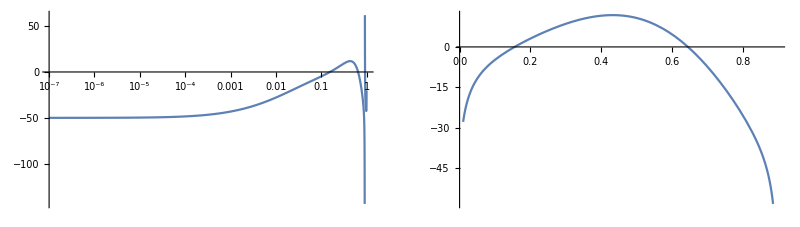

```mathematica
(* Relative difference *)
avgtot3 = Mean[ggq3inv3cherries];
f = (avgtot3 + ggq3asy3 - ggq3nf3x)/ggq3nf3x * 100;
r1 = Plot[f, {x, 0.01, 0.9}];
r2 = LogLinearPlot[f, {x, 10^-7, 1} ];
GraphicsRow[{r2,r1}]
```

#### Interpolation checks

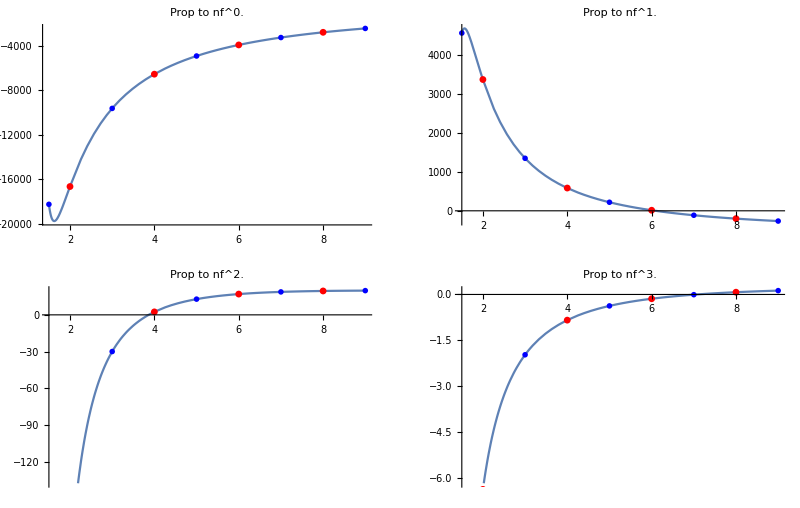

```mathematica
ggq3asytmp = ggq3N0asy + ggq3N1asyImproved + ggq3Ninf;
GraphicsGrid[{
	{PlotInterpolation[ggqmoments, {1.5, 3,5,7,9}, 0], PlotInterpolation[ggqmoments -ggq3asytmp, {1.5,3,5,7,9}, 1]},
	{PlotInterpolation[ggqmoments - ggq3asytmp, {1.5, 3,5,7,9}, 2], PlotInterpolation[ggqmoments -ggq3asytmp, {1.5,3,5,7,9}, 3]}
}, ImageSize->Full, PlotRange->All]
```

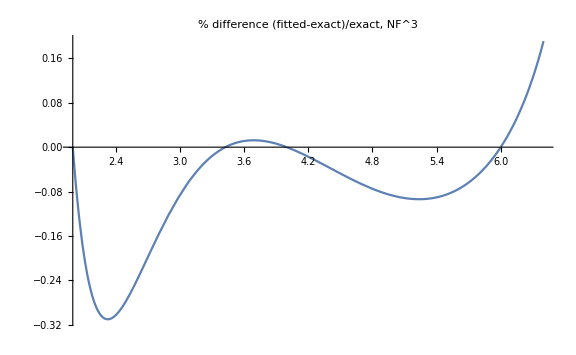
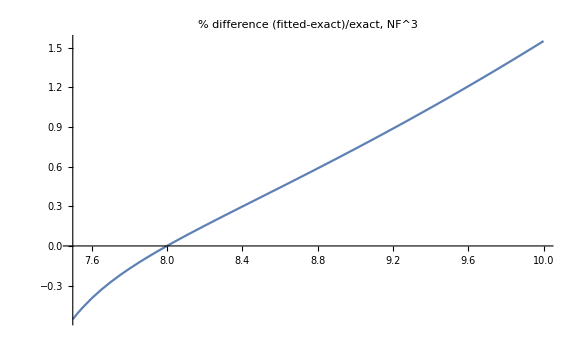

```mathematica
interpolator = MomentListInterpolator[ggqmoments, {2, 4, 6, 8}, 3];
{PlotRelativeDiff[ggq3nf3, nf^3 interpolator, 3, 2, 6.4],PlotRelativeDiff[ggq3nf3, nf^3 interpolator, 3, 7.5, 10]}
```

#### Fixing N = 3

Part::partw: Part 2 of #1 does not exist.

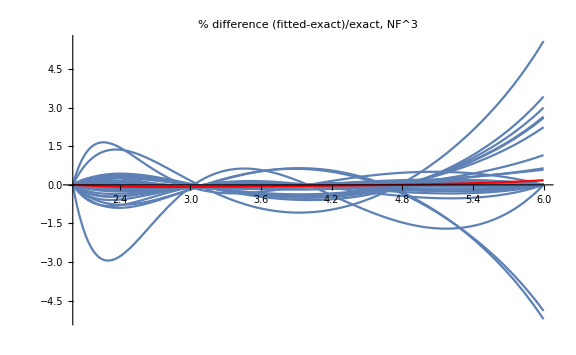

```mathematica
flargeN = {{S13m1[n], S12m1[n]},{S13m1[n], S12m1[n]},{S13m1[n],  S12m1[n]}, {S13m1[n], S12m1[n]}};
fSubLeadingLargeN = { 
	{1/(n+1),1/(n+1),1/(n+1),1/(n+1)},
	{1/(n+2),1/(n+2),1/(n+2),1/(n+2)}, 
	{1/(n+1)^2,1/(n+1)^2,1/(n+1)^2,1/(n+1)^2}, 
	{1/(n+1)^3,1/(n+1)^3,1/(n+1)^3,1/(n+1)^3}, 
	{Lm11[n],Lm11[n],Lm11[n], Lm11[n]}, 
	{Lm12[n],Lm12[n],Lm12[n], Lm12[n]}, 
	{Lm13[n],Lm13[n],Lm13[n], Lm13[n]}
};
fSubLeading = Join[fSubLeadingSmallN, fSubLeadingLargeN];

ggq3FittedInterpol = InterploatedFit[fsmallN, flargeN, fSubLeading, ggqmoments, ggq3N0asy, ggq3N1asyImproved, ggq3Ninf, {3}];
PlotRelativeDiffIterate[ggq3nf3 - Coefficient[ggq3N0asy + ggq3N1asyImproved + ggq3Ninf, nf ,3], ggq3FittedInterpol, 3, 2, 6]
```

```mathematica
ggq3invinterpol = ListMellinInverse[ggq3FittedInterpol];
ggq3invinterpol = SelectSmoothCandidates[ggq3invinterpol, 4,thrlow,thrlow];
```

Smooth candidates: 62 out of 66

```mathematica
GraphicsRow[ShowPlots[ggq3inv, ggq3invinterpol, ggq3asy, 4, {"cross candidates", "N=3"}], ImageSize -> Full]
```

-Graphics-

#### Fixing N = 3 and n=5

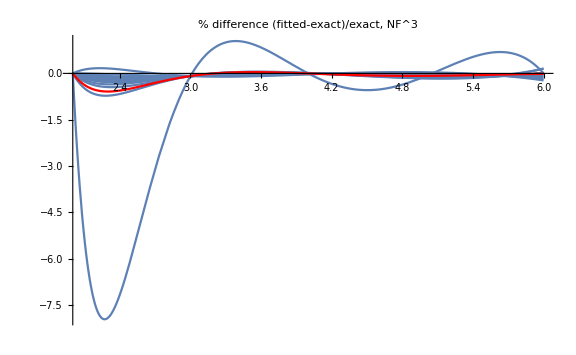

```mathematica
flargeN = {{S13m1[n], S12m1[n], S[1,n-2]/n},{S13m1[n], S12m1[n], S[1,n-2]/n},{S13m1[n],  S12m1[n],S[1,n-2]/n}, {S13m1[n], S12m1[n], Lm11[n]}};
fSubLeadingLargeN = { 
	{Lm13[n],Lm13[n],Lm13[n], Lm13[n]},
	{1/(n+1),1/(n+1),1/(n+1), 1/(n+1)}
};
fSubLeading = Join[fSubLeadingSmallN, fSubLeadingLargeN];

ggq3FittedInterpol2 = InterploatedFit[fsmallN, flargeN, fSubLeading, ggqmoments, ggq3N0asy, ggq3N1asyImproved, ggq3Ninf, {3,5}];
PlotRelativeDiffIterate[ggq3nf3 - Coefficient[ggq3N0asy + ggq3N1asyImproved + ggq3Ninf, nf ,3], ggq3FittedInterpol2, 3, 2, 6]
```

```mathematica
ggq3invinterpol2 = ListMellinInverse[ggq3FittedInterpol2];
ggq3invinterpol2 = SelectSmoothCandidates[ggq3invinterpol2, 4,thrlow,thrlow];
```

Smooth candidates: 20 out of 21

```mathematica
GraphicsRow[ShowPlots[ggq3inv, ggq3invinterpol2, ggq3asy, 4, {"cross candidates", "N=3 and N=5"}], ImageSize -> Full]
```

-Graphics-

#### Save and final remove

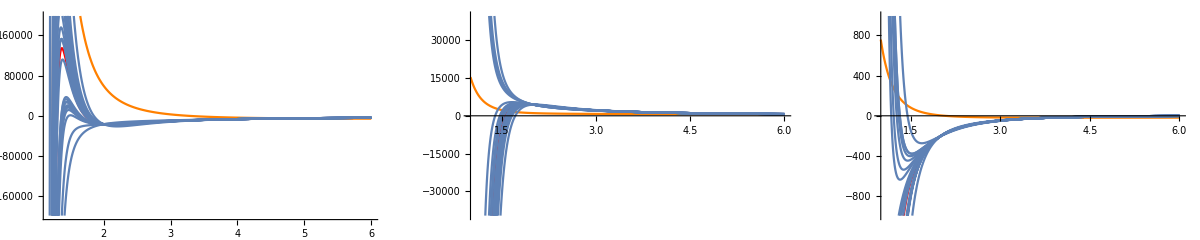

```mathematica
smoothcherryn = ggq3FittedCross[[Position[ggq3invfull, #]& /@ ggq3cherry //Flatten]] /. largeNrules // Simplify;
ggq3Nasy = ggq3N0asy + ggq3N1asyImproved + ggq3Ninf;
g0 = PlotListN[ggq3Nasy, smoothcherryn, 0, -100 * (4 Pi)^3, 100 * (4 Pi)^3];
g1 = PlotListN[ggq3Nasy, smoothcherryn, 1, -20 * (4 Pi)^3, 20 * (4 Pi)^3];
g2 = PlotListN[ggq3Nasy, smoothcherryn, 2, -0.5 * (4 Pi)^3, 0.5 * (4 Pi)^3];
GraphicsRow[{
	Show[g0, PlotRange-> All],
	Show[g1, PlotRange-> All],
	Show[g2, PlotRange-> All]
}, ImageSize->Full]
```

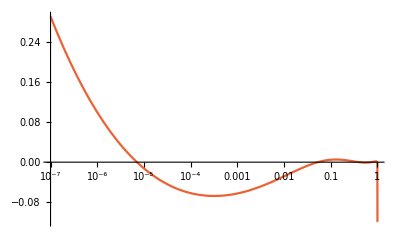
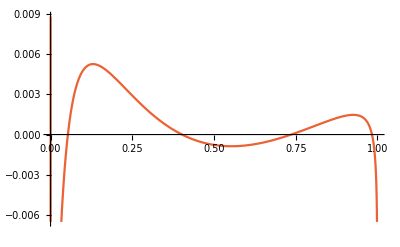
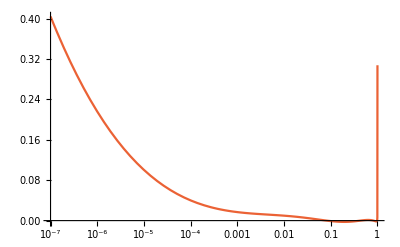
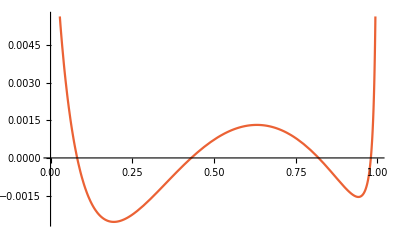
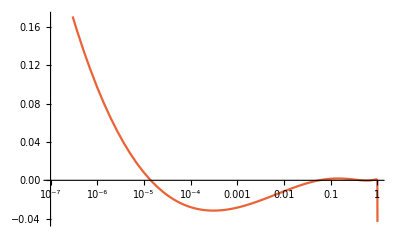
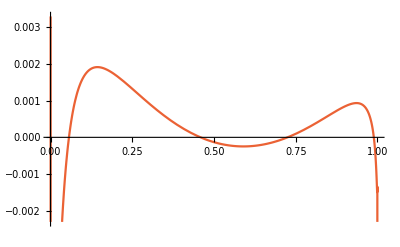
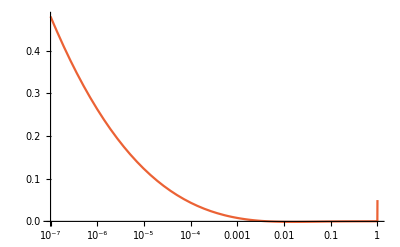
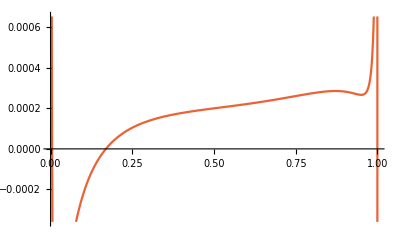
{{1,-Graphics-,-Graphics-},{2,-Graphics-,-Graphics-},{3,-Graphics-,-Graphics-},{4,-Graphics-,-Graphics-},{5,-Graphics-,-Graphics-},{6,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{8,-Graphics-,-Graphics-},{9,-Graphics-,-Graphics-},{10,-Graphics-,-Graphics-},{11,-Graphics-,-Graphics-},{12,-Graphics-,-Graphics-},{13,-Graphics-,-Graphics-},{14,-Graphics-,-Graphics-},{15,-Graphics-,-Graphics-},{16,-Graphics-,-Graphics-},{17,-Graphics-,-Graphics-},{18,-Graphics-,-Graphics-},{19,-Graphics-,-Graphics-},{20,-Graphics-,-Graphics-},{21,-Graphics-,-Graphics-},{22,-Graphics-,-Graphics-},{23,-Graphics-,-Graphics-},{24,-Graphics-,-Graphics-}}

```mathematica
MapThread[{#1, #2, #3} &, {Range[1, graphGQlogcherryrep // Length], graphGQlogcherryrep, graphGQcherryrep}]
```

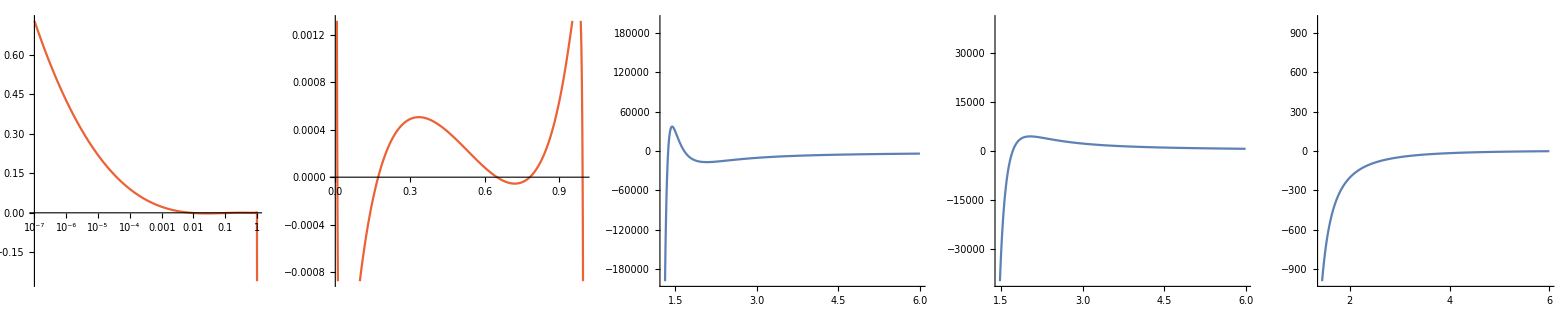

-56096.8/(-1.+n)+94447.4 S2m2-30904. S12m1[n]+nf (-21387.2 S2m2+17430.9 S3m2+5100.18 S12m1[n]-1401.39 S13m1[n])+nf^3 (-9.29007/(-1.+n)+3.93392 S12m1[n]-0.894849 S13m1[n])+8763.72 S13m1[n]+nf^2 (-210.675/(-1.+n)+205.245 S2m2-6.83729 S12m1[n]+7.04795 S13m1[n])

```mathematica
posix=12;
GraphicsRow[{graphGQlogcherryrep[[posix]], graphGQcherryrep[[posix]], g0[[posix+1]], g1[[posix+1]], g2[[posix+1]]}, ImageSize->Full]
smoothcherryn[[posix]]
```

```mathematica
ggq3cherryrefined = ggq3cherry;
graphGQcherryrepref = PlotList[ggq3cherryrefined, ggq3asy, 4, 4];
graphGQlogcherryrepref = LogPlotList[ggq3cherryrefined, ggq3asy, 4, 4];
GraphicsRow[{graphGQlogcherryrepref // Show, Show[graphGQcherryrepref, PlotRange -> {Automatic, {-0.01, 0.01}}]}]
```

-Graphics-

```mathematica
{graphGQcherry1, graphGQcherrylog1} = PlotErrorBand[ggq3asy, ggq3cherryrefined, 4, 4]; 
legend = {"cross candidate", "cherries"}; 
GraphicsRow[{
      	ShowLegends[{graphGQlog, graphGQcherrylog1}, LogLinearPlot, legend, {3, 4}], 
      	ShowLegends[{graphGQ, graphGQcherry1}, Plot, legend, {3, 4}]
      	}, ImageSize -> Full
  ]
```

-Graphics-

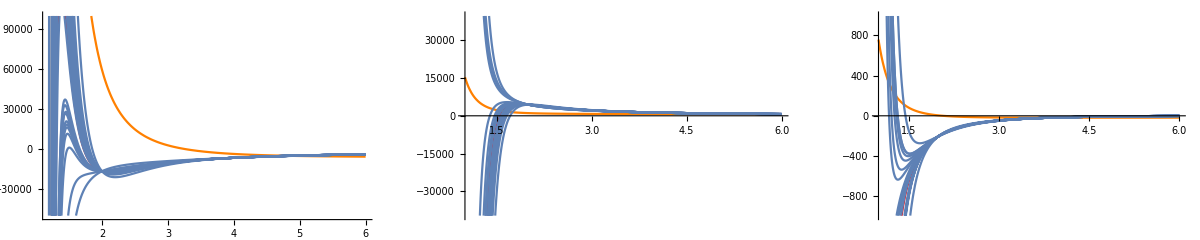

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/ggq3nf0.c

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/ggq3nf1.c

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/ggq3nf2.c

```mathematica
smoothcherryn = ggq3FittedCross[[Position[ggq3invfull, #]& /@ ggq3cherryrefined //Flatten]] /. largeNrules // Simplify;
g0 = PlotListN[ggq3Nasy, smoothcherryn, 0, -50000, 100000];
g1 = PlotListN[ggq3Nasy, smoothcherryn, 1, -20 * (4 Pi)^3, 20 * (4 Pi)^3];
g2 = PlotListN[ggq3Nasy, smoothcherryn, 2, -0.5 * (4 Pi)^3, 0.5 * (4 Pi)^3];
GraphicsRow[{
	Show[g0, PlotRange-> All],
	Show[g1, PlotRange-> All],
	Show[g2, PlotRange-> All]
}, ImageSize->Full]
exportMeList[ggq3Nasy, smoothcherryn, StringJoin[storepath, "ggq3nf0.c"], 0];
exportMeList[ggq3Nasy, smoothcherryn, StringJoin[storepath, "ggq3nf1.c"], 1];
exportMeList[ggq3Nasy, smoothcherryn, StringJoin[storepath, "ggq3nf2.c"], 2];
```

```mathematica
smoothcherryn//Length
```

24

#### Test small-x limit, when fitting NLL term

At LL we have  that gq = cf /ca gg

```mathematica
gqll = Coefficient[ggq3N1asy, (n-1), -4];
ggll = Coefficient[ggg3N1asy, (n-1), -4];
(ggll/gqll) (cf/ca)
```

1

Test how much this scaling is violated at NLL by the best fit.
Clearly the parametrize solution is too small to recover the scaling.
From what we can guess from NNLO, at least the part proportional to nf^0,
do not violate the scaling more than 3% .

```mathematica
(* Best fit extracted from python file ggq.py on commit 0391ddc0 *)
bestfitgq = -57163.2924910954 S[3, n-2]/n + (2607.6807899256582 S[3, n-2]/n)/(-1+ n) - (2607.6807899256582 n S[3, n-2]/n)/(-1 + n);
bestfitgqnll = Coefficient[Series[bestfitgq  /. InverseHarmonicRules , {n,1,0}], (n-1),-3];
ggnll = Coefficient[ggg3N1asy, (n - 1), -3];
(ggnll / bestfitgqnll) (cf / ca) /. nf -> 0 /. QCDConstantsRules /. ZetaRules // Simplify
```

1.58995

Check how large is the coefficient of NLL/LL both in P_gg and in the best fit P_gq.
Also from here we see that the NLL/LL ratio is too small to recover the natural scaling.

```mathematica
ggnll /ggll/. QCDConstantsRules /. ZetaRules // Simplify//Expand//N
bestfitgqnll /gqll/. QCDConstantsRules /. ZetaRules // Simplify//Expand//N
```

-4.2892-0.0399739 nf

-2.69769

#### Small N and large N checks

```mathematica
(* w/o fitting the 1/(n-1)^3 coeff *)
fsmallNtmp = {S[2,n-2]/n, S[2,n-2]/n, S[1,n-2]/n, S[1,n-2]/n};
fSubLeadingSmallNtmp = {
	{1/(n-1),1/(n-1),1,1}, 
	{1/n^4,1/n^4,1/n^4,1/n^4},
	{1/n^3,1/n^3,1/n^3,1/n^3},
	{1/n^2,1/n^2,1/n^2,1/n^2},
	{1/n,1/n,1/n,1/n,1/n}
};
fSubLeadingtmp = Join[fSubLeadingSmallNtmp, fSubLeadingLargeN];
ggq3asytmp = MellinInverseSinglet[ggq3N0asy + cf/ ca * ggg3N1asy + ggq3Ninf] /. Delta[x__] -> 0 /. LimitRules /. ZetaRules;
ggq3FittedCross1 = DoAllFits[fsmallNtmp, flargeN, fSubLeadingtmp, ggqmoments, ggq3N0asy, cf/ ca * ggg3N1asy, ggq3Ninf];

(* change large-N leading term *)
flargeNtmp = {1/(n+1), 1/(n+1),1/(n+1),1/(n+1)};
ggq3FittedCross2 = DoAllFits[fsmallN, flargeNtmp, fSubLeadingtot, ggqmoments, ggq3N0asy, ggq3N1asyImproved, ggq3Ninf];
```

```mathematica
ggq3inv1 = ListMellinInverse[ggq3FittedCross1];
ggq3inv1 = SelectSmoothCandidates[ggq3inv1, 4,thrlow,thrlow];
ggq3inv2 = ListMellinInverse[ggq3FittedCross2];
ggq3inv2 = SelectSmoothCandidates[ggq3inv2, 4,thrlow,thrlow];
```

Smooth candidates: 75 out of 78

Smooth candidates: 88 out of 91

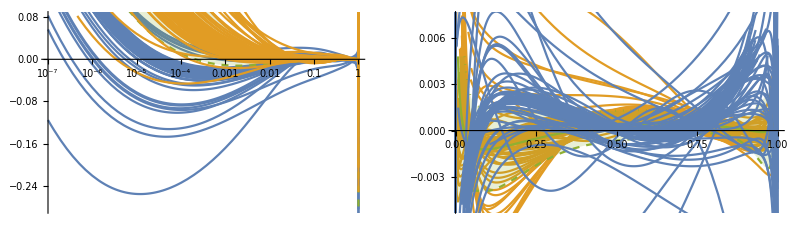

```mathematica
graphGQ1 = PlotList[ggq3inv1, ggq3asytmp, 4, 1] // Show;
graphGQ1log = LogPlotList[ggq3inv1, ggq3asytmp, 4, 1] // Show;
graphGQ2 = PlotList[ggq3inv2, ggq3asy, 4, 2] // Show;
graphGQ2log = LogPlotList[ggq3inv2, ggq3asy, 4, 2] // Show;

GraphicsRow[{Show[{graphGQ1log, graphGQlog,graphGQ2log}], Show[{graphGQ2, graphGQ, graphGQ1}]}]
```

```mathematica
{graphGQ1, graphGQ1log}= PlotErrorBand[ggq3asytmp, ggq3inv1, 4, 1];
{graphGQ2, graphGQ2log}= PlotErrorBand[ggq3asy, ggq3inv2, 4, 2];

legend = {"w/o fitting 1/(n-1)^3", "fitting 1/(n-1)^3", "large-N change"};
GraphicsRow[{
	ShowLegends[{graphGQ1log, graphGQlog, graphGQ2log}, LogLinearPlot, legend, {1,3,2}],
	ShowLegends[{graphGQ1,graphGQ,graphGQ2}, Plot, legend, {1,3,2}]
	}, ImageSize -> Full
]
```

-Graphics-